# Cavity extraction and atom-photon entanglement rates

P. Huft

To-do: check that my results are in agreement with Akbar’s paper. 

Quantum efficiency for optical cavities used as photon collectors, Purcell effect, photon collection comparison between cavity and free space, entanglement rate calculations for atom-photon and (trivially) subsequent atom-atom entanglement.

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
imag[z_]:=(z-conj[z])/2;
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[PolarPlot,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{Drop[Table[i,{i,0,2 Pi,Pi/4}],-1],Automatic},LabelStyle->Directive[Black, 16],ImageSize->Medium];
ppm = 10^-6;
```

## Single atom in a cavity - system characterization

### Mark’s example 1 - short confocal cavity

Algebra confirmed by hand, results agree with Mark if 87 RbD1 line assumed.

```mathematica
(*CAVITY PARAMS*)
L=1.5*^-4;(*cavity length*)
RoC = L;
F =3*^4;(* (π (R1 R2)^(1/4))/(1-(R1 R2)^(1/2))cavity finesse*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = 4.3*^-6;(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = 2.992 e a0/√2; (*D1*)
Γ = 2π 5.746*^6;(*ΓD2*); (*atom decay rate, e.g. 87Rb 5P3/2*)
λ = 7.95*^-7;(*λD2*);
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{4.3×10^-6,0.00015,30000,9.99567×10^11,3.28844×10^8}

Atom d [a.u.], Γ/(2π), λ:

{2.11566,5.746×10^6,7.95×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

4.87596×10^7

Cooperativity, confocal [dimensionless]:

24.1965

Fractional emission into cavity mode:

0.979754

Quantum efficiency:

0.835644

Compare w/ Mark’s result:

```mathematica
Cooperativity/23.9
```

1.0124

```mathematica
g/(2π 4.92*^7)
```

0.991048

### Short confocal cavity - medium finesse

The first “Carlos-style” fiber Fabry-Perot built by the Goldsmith group. Built by Beau and Carlos. The RoC and T values below are guesses. They didn’t actually report these values, but we have some idea of the batch the fibers came from.

```mathematica
(*CAVITY PARAMS*)
λ=7.8*^-7;
(*L=9*^-5;*)(*cavity length*)
Tin =160 ppm;
Tout= 20 ppm;(*cavity mirror transmission*)
RoC = 2.5*^-4;(*ablated fiber mirror radius of curvature*)
F =18*^3;(*cavity finesse, measured by Garrett 2019.07.26*)
(*FSR = c/(2L)*);(*free spectral range*)
κ =2π*94*^6; (*2π FSR/F;*) (*cavity linewidth or decay rate*)
FSR =F κ/(2π);
L=c/(2FSR);
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/4;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR//N, κ/(2π)//N}
(*ATOM PARAMS*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0)//N, Γ/(2π)//N,λ//N}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Tin/(Tin+Tout)
```

Cavity w0, L, F, FSR, κ/(2π):

{3.31672×10^-6,0.0000886141,18000,1.692×10^12,9.4×10^7}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

2.34987×10^8

Cooperativity, confocal [dimensionless]:

96.8123

Fractional emission into cavity mode:

0.994862

Quantum efficiency:

0.830715

Parameters for “gen 3” of the fiber Fabry-Perot built by the Goldsmith group

```mathematica
(*CAVITY PARAMS*)
L=1.2*^-4;(*cavity length*)
Tin =Tout= 20 ppm;(*cavity mirror transmission*)
RoC = 2.475*^-4;(*ablated fiber mirror radius of curvature*)
F =8.3*^3;(*cavity finesse, measured by Garrett 2019.07.26*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/4;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/(2π)}
(*ATOM PARAMS*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Tin/(Tin+Tout)
```

Cavity w0, L, F, FSR, κ/(2π):

{3.86025×10^-6,0.00012,8300.,1.24946×10^12,1.50537×10^8}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

1.73499×10^8

Cooperativity, confocal [dimensionless]:

32.9653

Fractional emission into cavity mode:

0.985059

Quantum efficiency:

0.473452

```mathematica
(g/Γ)^2
```

409.049

```mathematica
g^2/(κ Γ)
```

16.4827

For gen1 of the ferrule-based fiber cavity

```mathematica
(*CAVITY PARAMS*)
L=1.65*^-4;(*cavity legth*)
Tin =1600 ppm;
Tout= 20 ppm;(*cavity mirror transmission*)
RoC = 2.475*^-4;(*ablated fiber mirror radius of curvature, assuming same as previously*)
F =10*^3;(*cavity finesse, measured by Carlos 2022.05*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π));(*Confocal waist*)
V = (π w0^2 L)/4;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/(2π)}
(*ATOM PARAMS*)
d = D2MatElem; 
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Tin/(Tin+Tout)
```

Cavity w0, L, F, FSR, κ/(2π):

{4.52654×10^-6,0.000165,10000,9.08697×10^11,9.08697×10^7}

Atom d [a.u.], Γ/(2π), λ:

{4.2344,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

1.26181×10^8

Cooperativity, confocal [dimensionless]:

28.8853

Fractional emission into cavity mode:

0.982985

Quantum efficiency:

0.910097

```mathematica
κ/(2π)
```

9.08697×10^7

### Long near-concentric asymmetric cavity

Parameters for future near-conc. cavity to be built by the Goldsmith group

```mathematica
(*CAVITY PARAMS*)
L=3.99*10^-3;(* cavity length*)
RoC = 2*10^-3;(*mirror radius of curvature*)
Tlow = 10;(*mirror transmission ppm*)
Thigh = 4100;(*mirror transmission ppm*)
Lrt = 40;(*round trip loss, ppm*)
FSR = c/(2L);(*free spectral range*)
F = 2π/(-Log[(1-Tlow*10^-6)(1-Thigh*10^-6)(1-Lrt*10^-6)])//N;
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π))((RoC-L/2)/(L/2))^(1/4);(*Near-concentric waist*)
V = (π w0^2 L)/4;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = D2MatElem √(2*1/2+1)ClebschGordan[{1,-1},{1,1},{0,0}]/(√(2*3/2+1)); (*hyperfine transition dipole matrix element*)
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, near-concentric [dimensionless]:"
Cooperativity = 2 g^2/(κ Γ)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Thigh/(Thigh+Tlow+Lrt)
```

Cavity w0, L, F, FSR, κ/(2π):

{0.00563837 √λ,0.00399,1510.95,3.75777×10^10,2.45459×10^8}

Atom d [a.u.], Γ/(2π), λ:

{1.72869,6.0659×10^6,7.80241×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

9.52081×10^6

Cooperativity, near-concentric [dimensionless]:

1.20172

Fractional emission into cavity mode:

0.70618

Quantum efficiency:

0.560873

```mathematica
(*CAVITY PARAMS*)
L=9.99*10^-3;(* cavity length*)
RoC = 5*10^-3;(*mirror radius of curvature*)
Tlow = 10;(*mirror transmission ppm*)
Thigh = 4100;(*mirror transmission ppm*)
Lrt = 40;(*round trip loss, ppm*)
FSR = c/(2L);(*free spectral range*)
F = 2π/(-Log[(1-Tlow*10^-6)(1-Thigh*10^-6)(1-Lrt*10^-6)])//N;
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = √((λ L)/(2 π))((RoC-L/2)/(L/2))^(1/4);(*Near-concentric waist*)
V = (π w0^2 L)/4;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = D2MatElem √(2*1/2+1)ClebschGordan[{1,-1},{1,1},{0,0}]/(√(2*3/2+1)); (*hyperfine transition dipole matrix element*)
Γ =ΓD2; (*atom decay rate, e.g. 87Rb 5P3/2*)
λ =λD2;
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, near-concentric [dimensionless]:"
Cooperativity = 2 g^2/(κ Γ)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
QE=(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Thigh/(Thigh+Tlow+Lrt)
```

Cavity w0, L, F, FSR, κ/(2π):

{0.00709253 √λ,0.00999,1510.95,50.0501 c,0.326929 c}

Atom d [a.u.], Γ/(2π), λ:

{D2MatElem/(√6 a0 e),ΓD2/(2 π),λD2}

Vacuum Rabi frequency g/(2π) [Hz]:

(183.312 D2MatElem √((c ℏ)/(ϵ0 λD2^2)))/ℏ

Cooperativity, near-concentric [dimensionless]:

(1.27478×10^7 D2MatElem^2)/(ΓD2 ϵ0 λD2^2 ℏ)

Fractional emission into cavity mode:

(2.54957×10^7 D2MatElem^2)/(ΓD2 ϵ0 λD2^2 (1+(2.54957×10^7 D2MatElem^2)/(ΓD2 ϵ0 λD2^2 ℏ)) ℏ)

Quantum efficiency:

(5.24247×10^6 c D2MatElem^2)/(ΓD2 (0.20813 c+ΓD2) ϵ0 λD2^2 (1+(2.54957×10^7 D2MatElem^2)/(ΓD2 ϵ0 λD2^2 ℏ)) ℏ)

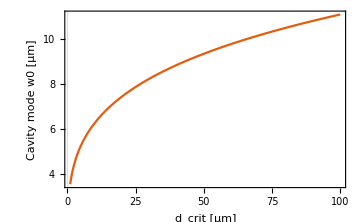

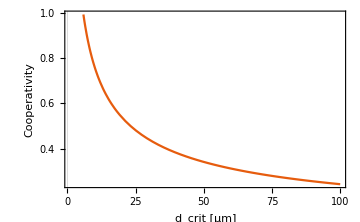

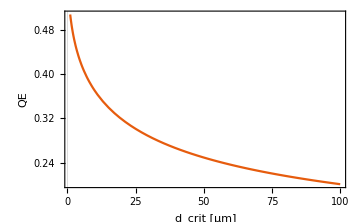

```mathematica
Clear[L]
w0 = √((λ L)/(2 π))((RoC-L/2)/(L/2))^(1/4);(*Near-concentric waist*)
Plot[10^6 w0/.L->2RoC-10^-6 dcrit,{dcrit,1,100},PlotTheme->"Scientific",FrameLabel->{"d_crit [μm]","Cavity mode w0 [μm]"}]
V = (π w0^2 L)/4;(*TEM00 mode volume*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
Cooperativity = 2 g^2/(κ Γ);
QE=(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)Thigh/(Thigh+Tlow+Lrt);
Plot[Cooperativity/.L->2RoC-10^-6 dcrit,{dcrit,1,100},PlotTheme->"Scientific",FrameLabel->{"d_crit [μm]","Cooperativity"}]
Plot[QE/.L->2RoC-10^-6 dcrit,{dcrit,1,100},PlotTheme->"Scientific",FrameLabel->{"d_crit [μm]","QE"}]
(*Plot[QE/.w0->10^-6 w,{w,3,10},PlotTheme->"Scientific",FrameLabel->{"Cavity mode w0 [μm]","Cooperativity"}]*)
```

```mathematica
(*cavity waists for various lengths*)
Clear[L,w0];
Lnom=10^-2;
"waist [μm], L/2 [mm], dcrit [μm]:"
Table[{w0,halfLmm=Values[NSolve[√((λ L)/(2 π))((RoC-L/2)/(L/2))^(1/4)==w0 10^-6,L]][[1,1]]/2*10^3//N,(2RoC-2halfLmm*10^-3)/10^-6},{w0,{5,7,10,13.5,15}}]
```

waist [μm], L/2 [mm], dcrit [μm]:

{{5,4.99797,4.05469},{7,4.9922,15.5945},{10,4.96736,65.2749},{13.5,4.88988,220.247},{15,4.83008,339.847}}

### Cooperativity Trade-off

See Meschede paper “Strong Purcell effect on a neutral atom....”. Note that what follows applies specifically to the case of equilibrium when an atom in a cavity is being driven continuously with an external field of Rabi freq. Ω.

```mathematica
coop = g^2/(2κ γ);
Ccoop = g^2/(2(κ-ⅈ Δc)(γ-ⅈ Δa));(*complex coop. see supplemental*)
Rfs=Ω^2/(2γ(1+Δa^2/γ^2))1/((1+2Ccoop)*conj[(1+2Ccoop)]);
Rc = (Ω^2 Ccoop*conj[Ccoop])/(γ coop(1+2 Ccoop)*conj[(1+2Ccoop)]);
```

```mathematica
Δa = Δc=0; (*cavity on tuned to atomic resonance, and probe tuned to cavity resonance
*)
```

```mathematica
Rfs
```

Ω^2/(2 γ (1+g^2/(γ κ))^2)

```mathematica
Rc
```

(g^2 Ω^2)/(2 γ^2 (1+g^2/(γ κ))^2 κ)

```mathematica
Clear[coop];
(Rfs+Rc)/.g^2/(2κ γ)-> coop//FullSimplify
```

(κ Ω^2)/(2 g^2+2 γ κ)

```mathematica
Rc = (Ω^2 coop)/(γ(1+2 coop)^2);
Rfs = Ω^2/(2γ(1+2 coop)^2);
```

```mathematica
Rtotal=Rc+Rfs//FullSimplify
```

Ω^2/(2 γ+4 coop γ)

```mathematica
Rfrac=Rc/Rtotal//FullSimplify
```

(2 coop)/(1+2 coop)

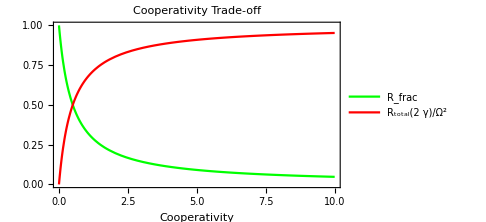

```mathematica
rTotal = 1/(1+2 coop);(*total atomic emission, Ω^2/γ = 1*)
rFrac = (2 coop)/(1+ 2 coop);(*fraction of emission into the cavity mode*)
plt=Plot[{rTotal,rFrac},{coop,0,10},PlotLegends->{"R_frac","R_total(2  γ)/Ω^2"}, PlotLabel->"Cooperativity Trade-off",FrameLabel->{"Cooperativity"}, ImageSize->Medium,PlotStyle->{Green,Red}]
```

```mathematica
Export[FileNameJoin[{imagedir,"cooperativity_tradeoff.png"}],plt]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\atomic_physics\images\cooperativity_tradeoff.png

### Strong coupling regime

Rachel Holdy thesis: both m0 and N0 should be < 1 for strong coupling.

```mathematica
"Critical photon number"
m0 = Γ^2/(2 g^2)(*critical photon number*)
"Critical atom number"
N0 = 1/Cooperativity (*critical atom number = 1/C*)
```

Critical photon number

0.00122235

Critical atom number

0.25178

### Enhanced emission

Feld paper. “The ratio of the spontaneous-emission rate into a single resonant cavity mode of quality factor Q and volume V to the total rate in free space is given by”

```mathematica
Q = (2π c/λ)/κ;
η=(3Q λ^3)/(4 π^2 V)(*depends only on solid angle and mirror reflectivity, not on λ/L*)
```

32.8078

## Atom collection - cavity vs free space

Comparison of photon collection from a single atom in a resonant cavity compared to an atom at the focus of a high NA lens. Also take into acct the overall rate of emission of the atom in the former case.

### ignoring atom perturbation

repeated pumping of the atom without a break for cooling may heat the push the atom out of the cavity mode volume or field of view of the lens; for now we will treat the atom as being stationary.

#### free space dipole emission pattern

```mathematica
λ = 7.8*10^-7;
k = 2π/λ;
unit[v_]:=v/(√(v.v));
(*GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));*)
```

spherical basis r, θ, ϕ. From Stephenson thesis, un-normalized polarization state. integration below freaks out and gives a bizarre result if i normalize the states.

```mathematica
pi ={0,-Sin[θ],0};
rh =ⅇ^(ⅈ ϕ)/(√2){0,Cos[θ],ⅈ};
lh =ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
```

Verify that the three states give equal contribution of polarization

```mathematica
Map[Integrate[#.conj[#] Sin[θ],{θ,0,π},{ϕ,0,2π}]&,{pi,lh,rh}]
norm = 1/%[[1]]
```

{(8 π)/3,(8 π)/3,(8 π)/3}

3/(8 π)

Verify the states are orthogonal

```mathematica
Integrate[rh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[pi] Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[lh.conj[rh] Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

0

0

0

```mathematica
plt=PolarPlot[{(lh.conj[lh]+rh.conj[rh])norm,pi.conj[pi]norm},{θ,0,2π},PlotLabel-> "Dipole emission pattern",PlotLegends->{"P(σ+ or σ-)","P(π)"},PlotStyle->{Green,Red}]
```

-Graphics-

```mathematica
(*Export[FileNameJoin[{imagedir,"dipole_emission.png"}],plt]*)
```

C:\Users\prest\OneDrive\Documents\amo-mathematica\atomic_physics\images\dipole_emission.png

The percentage of emitted circularly polarized photons which are collected by the lens is given by:

```mathematica
NA = 1;
θlens =ArcSin[NA];
Psigma=norm Integrate[(lh.conj[lh])Sin[θ],{θ,0,θlens},{ϕ,0,2π}]
```

1/2

```mathematica
NA = 0.5;
θlens =ArcSin[NA];
Psigma=norm Integrate[(pi.conj[pi])Sin[θ],{θ,0,θlens},{ϕ,0,2π}]
```

0.0128607

The fraction of emitted linear photons, which we do not want, but collect nonetheless is given by:

```mathematica
Plinear = norm Integrate[pi.conj[pi]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]
```

0.0128607

For the Rb D2 line F=0-> F=1 transition, with equal branching ratios among hyperfine states, 2/3 of the photons will be σ polarized, and hence the photons we want and those we do not have relative collection probabilities (normalized to total emission):

```mathematica
2/3 Psigma
```

0.00857381

```mathematica
1/3 Plinear
```

0.0042869

Sanity check: a 0.6 NA lens spans 10% of the solid angle, so we should collect 10% of all emission:

```mathematica
2/3 Psigma+1/3 Plinear
```

0.0128607

Taking into account fiber coupling efficiency η, the probability of reading a σ photon out of the fiber is

```mathematica
η = 0.9;
Pcollect=η 2/3 Psigma (*the probability of collecting a σ photon in the fiber. this is what we want to beat with a cavity*)
```

0.00771643

```mathematica
contrast = (2/3 Psigma -1/3 Pcollect)/(2/3 Psigma +1/3 Pcollect)
```

0.538462

Quantum efficiency vs NA: fraction of light collected by a lens, compared to what can be coupled into a single mode fiber given a suitable lens.

```mathematica
Clear[f,w,NA];σLensCollection=norm Integrate[lh.conj[lh] Sin[θ],{θ,0,ArcSin[NA]},{ϕ,0,2π}];
EGσ=(ⅇ^(-ρ^2/w^2))/(w √π){Cos[ϕ]+ⅈ Sin[ϕ],0,-(Sin[ϕ]-ⅈ Cos[ϕ])};Eσ=√(3/(16 π))(ⅈ ⅇ^(ⅈ ϕ) √f)/((f^2+ρ^2)^(3/4)){f/(√(f^2+ρ^2)),0,ⅈ};
ρNA=(f NA)/(√(1-NA^2));
Assuming[f>0&&NA>0,Integrate[ρ Abs[Eσ.conj[Eσ]]^2,{ρ,0,ρNA},{ϕ,0,2π}]]
```

$Aborted

Values::invrl: The argument 3/1024 is not a valid Association or a list of rules.

Values[ConditionalExpression[(3 (4 NA^6-3 NA^8))/(1024 f^2 π), NA<1]]

```mathematica
f=w/Tan[ArcSin[NA]];
ρNA=(f NA)/(√(1-NA^2));
NATable={0.2,0.6,0.9,0.95,0.98};
```

```mathematica
wTable=Table[Values[FindMaximum[Abs[Integrate[ρ EGσ.conj[Eσ],{ρ,0,ρNA},{ϕ,0,2π}]]^2,w][[2,1]]],{NA,NATable}]
```

{1.,1.,1.,1.,1.}

```mathematica
Clear[f,NA,w]
EGσ.conj[Eσ]//FullSimplify
```

(ⅈ √3 ⅇ^(-ρ^2/w^2) √f (f-√(f^2+ρ^2)))/(4 π w (f^2+ρ^2)^(5/4))

```mathematica
σFiberCollection={};
For[i=1,i<Length[NATable]+1,i++,
w=wTable[[i]];
NA=NATable[[i]];
AppendTo[σFiberCollection,Abs[Integrate[ρ EGσ.conj[Eσ],{ρ,0,ρNA},{ϕ,0,2π}]]^2];
]
```

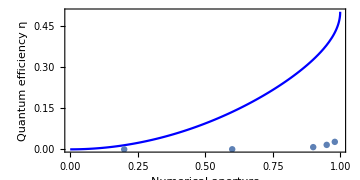

```mathematica
Show[Plot[σLensCollection,{NA,0,1},PlotPoints->100,FrameLabel->{"Numerical aperture","Quantum efficiency η"},AspectRatio->1.5,LabelStyle->Directive[Black,20],PlotStyle->{Orange,Blue},PlotRange->{0,0.5}],ListPlot[Transpose@@{{NATable,σFiberCollection}}],AspectRatio->1/2,PlotLegends->{"Lens","SM Fiber"}]
```

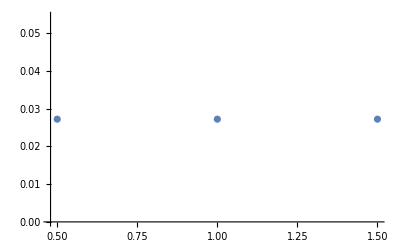

```mathematica
NA=0.98;
wRange = Range[.5,1.5,0.5];
ListPlot[Transpose@@{{wRange,Table[Abs[Integrate[ρ EGσ.conj[Eσ],{ρ,0,ρNA},{ϕ,0,2π}]]^2,{w,wRange}]}}]
```

```mathematica
Clear[f,w,NA];
EGσ=1/(w √π)ⅇ^(-ρ^2/w^2){Cos[ϕ]+ⅈ Sin[ϕ],0,Sin[ϕ]-ⅈ Cos[ϕ]};(*Circularly polarized Gaussian E-field mode*)
Eσ=√(3/(16 π))(ⅈ ⅇ^(ⅈ ϕ)f^(1/2))/((ρ^2+f^2)^(3/4)){f/((f^2+ρ^2)^(1/2)),0,ⅈ};(*σ emission from the atom after lens transformation*)
NA=0.6;
(*w=1;*)
f=w/NA;
ρNA=(f NA)/(√(1-NA^2));
σFiberCollection=Abs[Integrate[ρ (EGσ.conj[Eσ])/.w->Values[FindMaximum[EGσ.conj[Eσ],w][[2]]][[1]],{ρ,0,ρNA},{ϕ,0,2π}]]^2
```

1.

```mathematica
norm Assuming[NA∈Reals&&f∈Reals&&w∈Reals, Integrate[EGσ.conj[Eσ],{ρ,0,ρNA},{ϕ,0,2π}]]
```

$Aborted

```mathematica
EGσ.conj[Eσ]//FullSimplify
```

(ⅈ √3 ⅇ^(-ρ^2/w^2) √f (f+√(f^2+ρ^2)))/(4 π w (f^2+ρ^2)^(5/4))

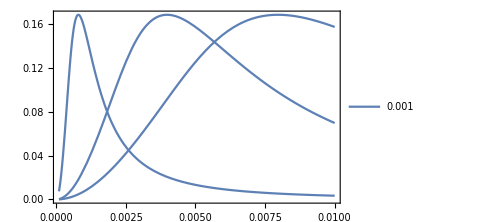

```mathematica
Clear[f,w,NA];
NA=0.7;
ρNA=(f NA)/(√(1-NA^2));
fTable={0.001,0.005,.01};
Plot[Table[Abs[NIntegrate[ρ(ⅈ √3 ⅇ^(-ρ^2/w^2) √f (f+√(f^2+ρ^2)))/(4 π w (f^2+ρ^2)^(5/4)),{ρ,0,ρNA},{ϕ,0,2π}]]^2,{f,fTable}],{w,10^-4,0.01},PlotLegends->fTable]
```

```mathematica
Clear[f,w,NA];
NA=0.5;
Table[FindMaximum[Abs[NIntegrate[ρ(ⅈ √3 ⅇ^(-ρ^2/w^2) √f (f+√(f^2+ρ^2)))/(4 π w (f^2+ρ^2)^(5/4)),{ρ,0,ρNA},{ϕ,0,2π}]]^2,{w,NA f}],{f,fTable}]
```

NIntegrate::inumr: The integrand ((0.+0.00435864 ⅈ) ⅇ^(-ρ^2/w^2) ρ (0.001+√(1.×10^-6+ρ^2)))/(w (1.×10^-6+ρ^2)^(5/4)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.00057735},{0,6.28319}}.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::inumr: The integrand ((0.+0.00974621 ⅈ) ⅇ^(-ρ^2/w^2) ρ (0.005+√(0.000025+ρ^2)))/(w (0.000025+ρ^2)^(5/4)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.00288675},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.0806721,{w→0.000495787}},{0.0806721,{w→0.00247896}},{0.0806721,{w→0.00495793}}}

```mathematica
fTable
```

{0.001,0.005,0.01}

```mathematica
0.0062993312813500735/0.01
```

0.629933

```mathematica
0.0031496600868085077/0.005
```

0.629932

```mathematica
0.002478963972115198/0.005
```

0.495793

```mathematica
0.0
```

```mathematica
0.0005*f
```

2.5×10^-6

#### free-space high NA lens vs cavity collection - atom atom entanglement rate calc

```mathematica
NA = 0.61;
θlens =ArcSin[NA];
lh =ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
ηlens=3/(8 π) Integrate[lh.conj[lh]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]; (*quantum efficiency for sigma light*)
ηcav = 0.37; (*10 mm near-conc cavity*)
```

```mathematica
ηlens
```

0.140656

```mathematica
(*Cavity entanglement rate calculation. differs from the paper in form.*)
l = 0.001; (*1 m*)
λatt = 1.091;(*attention in fiber, units km*)
ηdetect =Exp[-l/λatt]*0.7;(*fiber atten, SPCM eff. ignores mode-matching of cavity output to fiber*)
Paa = 0.5*ηdetect^2 ηcav^2;
ntotal =Floor[ 1/Paa+0.5];(*total number of tries to get one atom-atom entangled pair on average*)
nn1=10; (*tries without needing to re-cool the atom. not justified here.*)
nEpoch = Floor[ntotal/nn1+0.5];(*epoch = nn1 trials plus a cooling phase*)
Tcool = 0.1*10^-3; (*times in s*)
Tπ = 30*^-9;
Tdet=1*^-6; 
Tpump=6*^-6;
TMOT =0.5;
Tentangle = nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool);
Tlifetime=2;
Nentangles=Tlifetime/Tentangle;
"average attempt rate (incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1+TMOT/Nentangles)
"average attempt rate (not incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1)
"Paa, cavity"
Paa
"expected number of tries before atom-atom entanglement event"
ntotal
"excitations per cooling phase"
nn1
"epochs (number of nn1 attempts plus a cooling phase)"
nEpoch
"e-bits/s with mirror (incl. MOT/FORT loading)"
1/(nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool)+TMOT/Nentangles)
"e-bits/s with mirror (not incl. MOT/FORT loading)"
1/(nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool))
```

average attempt rate (incl. MOT/FORT loading)

6908.22

average attempt rate (not incl. MOT/FORT loading)

58719.9

Paa, cavity

0.0334791

expected number of tries before atom-atom entanglement event

30

excitations per cooling phase

10

epochs (number of nn1 attempts plus a cooling phase)

3

e-bits/s with mirror (incl. MOT/FORT loading)

1565.86

e-bits/s with mirror (not incl. MOT/FORT loading)

1957.33

```mathematica
(*Parabolic mirror entanglement rate calculation.*)
l = 0.001; (*1 m*)
λatt = 1.091;(*attention in fiber, units km*)
ηdetect =0.7Exp[-l/λatt]0.7;(*mode-matching of the mirror light to the fiber, fiber atten, spcm eff.*)
Paa = 0.5*ηdetect^2 ηlens^2;
ntotal =Floor[ 1/Paa+0.5];(*total number of tries to get one atom-atom entangled pair on average*)
nn1=15; (*tries without needing to re-cool the atom. not justified here.*)
nEpoch = Floor[ntotal/nn1+0.5];(*epoch = nn1 trials plus a cooling phase*)
Tcool = 0.1*10^-3; (*times in s*)
Tπ = 30*^-9;
Tdet=1*^-6; 
Tpump=6*^-6;
TMOT =0.5;
Tentangle = nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool);
Tlifetime=2;
Nentangles=Tlifetime/Tentangle;
"average attempt rate (incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1+TMOT/Nentangles)(*note: Akbar used 40kHz based on what Weinfurter and Rempe have done, instead of calculating this*)
"average attempt rate (not incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1)
"Paa, parabolic mirror"
Paa
"expected attempts before atom-atom entanglement event"
ntotal
"attempts per cooling phase"
nn1
"epochs (number of nn1 attempts plus a cooling phase)"
nEpoch
"e-bits/s with mirror (incl. MOT/FORT loading)"
1/(nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool)+TMOT/Nentangles)
"e-bits/s with mirror (not incl. MOT/FORT loading)"
1/(nEpoch(nn1(Tπ+Tdet+Tpump) + Tcool))
```

average attempt rate (incl. MOT/FORT loading)

688.778

average attempt rate (not incl. MOT/FORT loading)

73010.5

Paa, parabolic mirror

0.00237073

expected attempts before atom-atom entanglement event

422

attempts per cooling phase

15

epochs (number of nn1 attempts plus a cooling phase)

28

e-bits/s with mirror (incl. MOT/FORT loading)

139.068

e-bits/s with mirror (not incl. MOT/FORT loading)

173.834

### entanglement rate in a atom array with a SPAD array detector.

See Large array entanglement in Obsidian.

```mathematica
(*SPAD entanglement rate calculation. light is coupled to the detector in free space*)
NA = 0.55; (*the highest NA JenOptik objectives we have*)
θlens =ArcSin[NA];
ηlens=norm Integrate[lh.conj[lh]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]; (*quantum efficiency for sigma light*)
ηdetect =0.15;(*SPAD eff at 780, e.g. the Pi Imaging SPAD512^2*)
Paa = 0.5*ηdetect^2 ηlens^2;
ntotal =Floor[ 1/Paa+0.5];(*total number of tries to get one atom-atom entangled pair on average*)
nn1=15; (*tries without needing to re-cool the atom/ion. not justified here.*)
nn = Floor[ntotal/nn1+0.5];(*epoch = nn1 trials plus a cooling phase*)
Tcool = 0.1*10^-3; (*times in s*)
Tπ = 30*^-9;
Tdet=1*^-6; 
Tpump=6*^-6;
TMOT =0.5;
Tentangle = nn(nn1(Tπ+Tdet+Tpump) + Tcool);
Nentangles=Tlifetime/Tentangle;
"average attempt rate (incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1+TMOT/Nentangles)(*note: Akbar used 40kHz based on what Weinfurter and Rempe have done*)
"average attempt rate (not incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1)
"Paa, high NA lens and free space coupling to SPAD"
Paa
"expected attempts before atom-atom entanglement event"
ntotal
"attempts per cooling phase"
nn1
"epochs (number of nn1 attempts plus a cooling phase)"
nn
"e-bits/s with mirror (incl. MOT/FORT loading)"
1/(nn(nn1(Tπ+Tdet+Tpump) + Tcool)+TMOT)
"e-bits/s with mirror (not incl. MOT/FORT loading)"
1/(nn(nn1(Tπ+Tdet+Tpump) + Tcool))
```

average attempt rate (incl. MOT/FORT loading)

212.858

average attempt rate (not incl. MOT/FORT loading)

73010.5

Paa, high NA lens and free space coupling to SPAD

0.000146198

expected attempts before atom-atom entanglement event

6840

attempts per cooling phase

15

epochs (number of nn1 attempts plus a cooling phase)

456

e-bits/s with mirror (incl. MOT/FORT loading)

1.68439

e-bits/s with mirror (not incl. MOT/FORT loading)

10.674

```mathematica
(*SPAD entanglement rate calculation. light is coupled to the detector in free space*)
NA = 0.7; (*the highest NA JenOptik objectives we have*)
θlens =ArcSin[NA];
ηlens=norm Integrate[lh.conj[lh]Sin[θ],{θ,0,θlens},{ϕ,0,2π}]; (*quantum efficiency for sigma light*)
ηdetect =0.15;(*SPAD eff at 780, e.g. the Pi Imaging SPAD512^2*)
Paa = 0.5*ηdetect^2 ηlens^2;
ntotal =Floor[ 1/Paa+0.5];(*total number of tries to get one atom-atom entangled pair on average*)
nn1=15; (*tries without needing to re-cool the atom/ion. not justified here.*)
nn = Floor[ntotal/nn1+0.5];(*epoch = nn1 trials plus a cooling phase*)
Tcool = 0.1*10^-3; (*times in s*)
Tπ = 30*^-9;
Tdet=1*^-6; 
Tpump=6*^-6;
TMOT =0.5;
Tentangle = nn(nn1(Tπ+Tdet+Tpump) + Tcool);
Nentangles=Tlifetime/Tentangle;
"average attempt rate (incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1+TMOT/Nentangles)(*note: Akbar used 40kHz based on what Weinfurter and Rempe have done*)
"average attempt rate (not incl. MOT/FORT loading)"
1/((Tπ+Tdet+Tpump) + Tcool/nn1)
"Paa, high NA lens and free space coupling to SPAD"
Paa
"expected attempts before atom-atom entanglement event"
ntotal
"attempts per cooling phase"
nn1
"epochs (number of nn1 attempts plus a cooling phase)"
nn
"e-bits/s with mirror (incl. MOT/FORT loading)"
1/(nn(nn1(Tπ+Tdet+Tpump) + Tcool)+TMOT)
"e-bits/s with mirror (not incl. MOT/FORT loading)"
1/(nn(nn1(Tπ+Tdet+Tpump) + Tcool))
```

average attempt rate (incl. MOT/FORT loading)

568.175

average attempt rate (not incl. MOT/FORT loading)

73010.5

Paa, high NA lens and free space coupling to SPAD

0.000392013

expected attempts before atom-atom entanglement event

2551

attempts per cooling phase

15

epochs (number of nn1 attempts plus a cooling phase)

170

e-bits/s with mirror (incl. MOT/FORT loading)

1.86942

e-bits/s with mirror (not incl. MOT/FORT loading)

28.6316

#### cavity mode volume derivation

Cavity mode volume:

```mathematica
Clear[w0,λ,L,k]
zR=π w0^2/λ;
k = 2π/λ;
 λ=2L/n; (*cavity resonance condition*)
mode = Exp[-ρ^2/w0^2]Sin[k z]; (*cavity mode Gaussian field profile, ignoring the axial dependence from the field expanding, as the Vuletic paper does. this overestimates the mode volume*)
volume =Integrate[2π mode^2 ρ,{ρ,0,∞},{z,-L/2,L/2},Assumptions->w0∈Reals&&zR∈Reals&&L∈Reals&&λ∈Reals&&n∈Integers]
```

```mathematica
1/4 L π w0^2
```

3.14159×10^-6 L

Now, don’t ignore the expansion of the field in the cavity:

```mathematica
Clear[w0,λ,L,k,n]
zR=π w0^2/λ;
k = 2π/λ;
λ=2L/n; (*cavity resonance condition*)
mode = 1/(√(1+z^2/zR^2))Exp[-ρ^2/(w0^2(1+z^2/zR^2))]Sin[k z]; (*cavity mode Gaussian field profile, ignoring the axial dependence from the field expanding, as the Vuletic paper does. this overestimates the mode volume*)
(*volume2=Integrate[2π mode^2 ρ,{ρ,0,∞},{z,-L/2,L/2},Assumptions->w0∈Reals&&λ∈Reals&&n∈Integers&&n∈Reals&&n>0&&λ>0&&w0>0]*)
```

The integral can be done by first doing the part over ρ, where i have used z-> z/zR and ρ->ρ/w0, and then integrating over the remaining function of z.

```mathematica
Integrate[(2π)/(1+z^2)Exp[(-2 ρ^2)/(1+z^2)]ρ,{ρ,0,∞},Assumptions-> z∈Reals]
```

π/2

```mathematica
volume2=π/2 w0^2 zR Integrate[Sin[k z zR]^2,{z,-1/zR L/2,1/zR L/2},Assumptions->w0∈Reals&&λ∈Reals&&n∈Integers&&n∈Reals&&n>0&&λ>0&&w0>0]
```

(L w0^2 (n π-Sin[n π]))/(4 n)

Which is simply 1/4 π w0^2 L as before. A simple thought experiment confirms it: perhaps the first mode expression, which ignores the expansion of the field in rho along as we defocus, is accurate when the beam is collimated in the cavity, and the resonator mirrors are near flat. Since the second mode expression, which takes into account the full nature of the field, must include fields which are nearly collimated, the two expressions ought to be equal. So the two integrals must agree, or the first one is assumed incorrect.

#### asymmetric concentric cavity collection

quantum efficiency calculated previously

```mathematica
ηcav =0.63;
```

#### symmetric confocal cavity collection

if a fiber resonator is not birefringent, the Purcell effect should act equally on all polarization states.

If the cavity is being weakly driven by an external field: The fractional emission goes up with cooperativity while the total emission goes down, so that the total emission collected by one end of the fiber resonator is

```mathematica
rTotal = ξ 1/(1+2 coop);(*total atomic emission, ξ=Ω^2/γ *)
rFrac = (2 coop)/(1+ 2 coop);(*fraction of emission into the cavity mode*)
PCollect = 2/3 Psigma rTotal rFrac
```

(0.181333 coop ξ)/(1+2 coop)^2

However if we are simply going to excite the atom and let it decay, the situation is a little different. The rate of spontaneous emission can actually be enhanced by a high Q cavity.

```mathematica
ηenh = (3Q)/(4 π^2)λ^3/V;(*Q, V the cavity quality and mode volume*)
```

Check the Feld paper’s expression to see if equation 1 is consistent with the enhancement factor.

## Single atom detection

### Resonant detection

Don’t care about how many photons required to detect the atom for small pump powers (large powers could heat the atom out of the detection region), but want N0 small, ~ 1. (Holdy thesis)

For an atom in a cavity, the absorption cross section scales as 1/mode area. For a coherent state illuminating the cavity, with mean photon number N0, we are trying to detect a change ΔN = N0 - N = N0 σ/ A.

#### Transmission SNR

Haase thesis derives an SNR formula which depends on the mean number of photons in the cavity: (eq 3.30, from steady state solution of Jaynes-Cummings treatment). Below I reproduce some relevant figures.

```mathematica
Clear[g,Γ,κ,n]
```

```mathematica
γ=(g^2 Γ)/(Γ^2+Δa^2+2 g^2 n);(*additional decay rate due to spontaneous scattering*)
U=(g^2 Δa)/(Γ^2+Δa^2+2 g^2 n);(*phase shift due to coherent scattering*)
η^2/((κ+γ)^2+(Δc-U)^2);(*implicit expression for mean number of photons. η is the cavity pumping rate, = Subscript[η, in] Subscript[t, 1], rate of incident photons times the input mirror transmission*)
```

Reproduce figure 3.3b from Haase thesis. jIn is photon flux/μs:

```mathematica
Clear[κT];
κlo=2π 6*10^6;
κ=κT+κlo;(*cavity losses from mirrors + scattering to other modes*)
g=2π *12*^6; (*vacuum Rabi frequency*)
Γ=ΓD2/2 ;(*they are using 87Rb D2 line, and their Γ is the half-width*)
τ=10^-5;(*measurement interval*)
steps=2π*10^6{0.8,1.5,2.3,3.1,3.8,7.7};(*κT steps in s^-1*)
data = {};
For[i=1,i<Length[steps]+1,i++,
κT=steps[[i]];
AppendTo[data,Table[{jIn,√(jIn *10^6 τ)κT/κ(1+γ/κ-1/(1+γ/κ))/.{Δa-> 0,Δc-> 0,n->NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(jIn*10^6 κT)},n,Reals][[1,1,2]]}},{jIn, Range[0,400,10]}]];
]
```

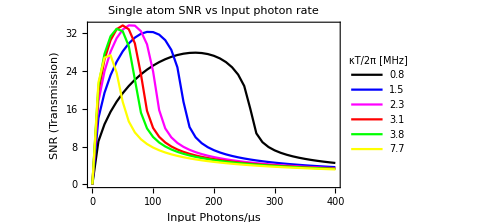

```mathematica
plt=ListPlot[data,PlotLabel-> "Single atom SNR vs Input photon rate",Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize-> 14],FrameLabel->{"Input Photons/μs","SNR (Transmission)"},PlotLegends->PointLegend[steps/(2π*10^6),LegendLabel-> "κT/2π [MHz]",LegendFunction->"Frame"],Joined->True,PlotStyle->{Black,Blue,Magenta,Red,Green,Yellow},ImageSize->Medium]
```

```mathematica
fname=FileNameJoin[{imagedir,"plot_haase_fig3pt3_.png"}];
Export[fname,plt];
```

Reproduce fig. 3.4 from Haase thesis. Similar to above but with broader cavity linewidth due to internal losses.

```mathematica
g=2π *12*^6; (*vacuum Rabi frequency*)
Γ=ΓD2/2 ;(*they are using 87Rb D2 line, and their Γ is the half-width*)
τ=10^-5;(*measurement interval*)
steps=2π*10^6{6,20,50,100,200,500};(*κlo steps in s^-1*)
data = {};
For[i=1,i<Length[steps]+1,i++,
κlo=steps[[i]];
κT = κlo/2;(*"mirror transmission rate was chosen to be optimal for every curve"*)
κ=κT+κlo;
AppendTo[data,Table[{jIn,√(jIn *10^6 τ)κT/κ(1+γ/κ-1/(1+γ/κ))/.{Δa-> 0,Δc-> 0,n->NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(jIn*10^6 κT)},n,Reals][[1,1,2]]}},{jIn, {0.25,0.5,1,2.5,5,10,25,50,75,100,250,500,1000,2500,5000,10000}}]];
]
```

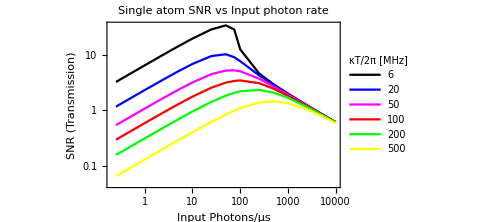

```mathematica
plt=ListLogLogPlot[data,PlotLabel-> "Single atom SNR vs Input photon rate",Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize-> 14],FrameLabel->{"Input Photons/μs","SNR (Transmission)"},PlotLegends->PointLegend[steps/(2π*10^6),LegendLabel-> "κT/2π [MHz]",LegendFunction->"Frame"],Joined->True,PlotStyle->{Black,Blue,Magenta,Red,Green,Yellow},ImageSize->Medium]
```

```mathematica
fname=FileNameJoin[{imagedir,"plot_haase_fig3pt4_.png"}];
Export[fname,plt];
```

```mathematica
NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η ->√(50*10^6 κT)},n,Reals]
```

{{n→0.00508289}}

Find transmission SNR for our cavity parameters

Obtain mean intra-cavity photon number numerically (run one of the cavity sections above to initialize g, Γ, κ):

```mathematica
Table[NSolve[n==η^2/((κ+γ)^2+(Δc-U)^2)/.{Δa-> 0,Δc-> 0,η -> √(κ (P 7.8*^-7)/(ℏ 2π c))},n],{P,{10^-9,10^-8,10^-7,10^-6,10^-4,10^-3}}](*mean photon number in cavity for different laser powers. the pump rate η is √(cavity decay rate *incident photons/s)*)
```

{{{n→0.497362},{n→-0.0012224+0.000120191 ⅈ},{n→-0.0012224-0.000120191 ⅈ}},{{n→5.01731},{n→-0.00122235+0.0000378837 ⅈ},{n→-0.00122235-0.0000378837 ⅈ}},{{n→50.2168},{n→-0.00122235+0.000011976 ⅈ},{n→-0.00122235-0.000011976 ⅈ}},{{n→502.211},{n→-0.00122235+3.78701×10^-6 ⅈ},{n→-0.00122235-3.78701×10^-6 ⅈ}},{{n→50221.6},{n→-0.00122235+3.787×10^-7 ⅈ},{n→-0.00122235-3.787×10^-7 ⅈ}},{{n→502216.},{n→-0.00122235+1.19755×10^-7 ⅈ},{n→-0.00122235-1.19755×10^-7 ⅈ}}}

Photon number exiting cavity in measurement duration τ:

```mathematica
10^19*κ *10^-6
```

7.85058×10^22

Mean rate of photons/s for coherent field with power P:

```mathematica
((10^-9 J/s)(7.8*10^-7 m))/((ℏ J s)(2π c m/s))*(1 s)/(10^6 μs)
```

3942.69/μs

Signal-to-noise ratio in units √(n_(out,0)), the sqrt of number of photons read out of an empty cavity:

plot this for several points. need to find n numerically at each step in power. try to produce something similar to figure 3.4 in Haase thesis

```mathematica
1+γ/κ-1/(1+γ/κ)/.{Δa-> 0,Δc-> 0,η -> √(κ (P 7.8*^-7)/(ℏ 2π c)),n-> get numerically}
```

9.70964×10^-7

## misc/scratchpad

```mathematica
(*power transmission for an apertured Gaussian beam*)
w0=5*^-6;
λ=7.8*^-7;
z=5*^-3+6.35*^-3;
zR=π w0^2/λ;
w=w0√(1+(z/zR)^2);
int=Exp[-2 ρ^2/w^2];
1-int /.ρ->1.5*^-3
```

0.999999

```mathematica
(*NA of a Gaussian beam*)
Clear[w0];
(*w0=5*^-6;*)
λ=7.8*^-7;
Table[{w0,λ/(π w0*10^-6)},{w0,2,20}]
```

{{2,0.124141},{3,0.0827606},{4,0.0620704},{5,0.0496563},{6,0.0413803},{7,0.0354688},{8,0.0310352},{9,0.0275869},{10,0.0248282},{11,0.0225711},{12,0.0206901},{13,0.0190986},{14,0.0177344},{15,0.0165521},{16,0.0155176},{17,0.0146048},{18,0.0137934},{19,0.0130675},{20,0.0124141}}

```mathematica
w
```

0.000248332

```mathematica
Integrate[int ρ,{ρ,0,2*^-3}]
```

1.54172×10^-8

```mathematica
Integrate[int ρ,{ρ,0,∞}]
```

1.54172×10^-8